## Opakování

1.)

Vytvořte graf s následujícími parametry:
Funkce:
	Sin[x]+Cos[y]
	(Cos[x]-Sin[y]) * 0.2
Rozsah:
	x ϵ <-2π, 2π>
	y ϵ <-2π, 2π >
PlotRange: osu „z" omezit <-1, 1>
PlotStyle: průhlednost druhé funkce 50%
Mesh: nezobrazovat na povrchu funkcí mřížku
ColorFunction: „Hue"
Boxed: nezobrazovat rámec kolem grafu
Axes: nezobrazovat osy grafu
Background: pozadí grafu libovolnou barvu

-Graphics3D-

2.)

Výpočet výrazu:

log_2 2-sin(π)+ⅇ^(π*ⅈ)

## Obsah hodiny

Funkce pro práci s textem

Textem v prostředí Wolfram Mathematica rozumíme řetězec znaků uvedený v uvozovkách.Jedná se o typ String.
Např.: “text”
	“Toto je nějaký text.”
	“A”
	“”

Mathematica obsahuje velké množství užitečných funkcí pro práci s textem z nichž se zaměříme na ty častěji používané.

### Style

Slouží k nastavení fontu (stylu) zadaného textu.

```mathematica
Style["Text"]
```

Text

```mathematica
Style["Text",
Bold(*tučný text*),
20(*velikost fontu*),
Red(*barva písma*)
]
```

Text

Pozn.: Můžeme pomocí funkce Style[] měnit nejen text, ale i různé grafické objekty.

```mathematica
Graphics3D[
Style[Cuboid[],
Red,
Opacity@0.5
]
,Boxed->False]
```

-Graphics3D-

### StringJoin

Spojení 2 a více stringů.

```mathematica
StringJoin["Ahoj.","Čau"]
```

Ahoj.Čau

Spojování textu můžeme psát i alternativně pomocí “<>”

```mathematica
"Ahoj."<>"Čau"
```

Ahoj.Čau

### StringSplit

Rozdělení textu.
Bez zadání druhého parametru rozděluje podle mezery.

```mathematica
StringSplit["Ahoj, jak se dnes máš?"]
```

{Ahoj,,jak,se,dnes,máš?}

```mathematica
StringSplit["AAaaAAbbcacbb","a"]
```

{AA,,AAbbc,cbb}

```mathematica
StringSplit["AAaaAAbbcacbb","aa"]
```

{AA,AAbbcacbb}

### StringLength

Vrací počet znaků v textovém řetězci.

```mathematica
StringLength["Ahoj"]
```

4

### StringTake | Drop | Delete

Skupina funkcí pro práci s textovým řetězcem (“vyseknutí” části textu).
Tyto funkce pracují téměř identicky s textem jako sesterských (Take|Drop|Delete) s vektory.

```mathematica
StringTake["Ahoj",2]
```

Ah

```mathematica
StringTake["Ahoj",-2]
```

oj

```mathematica
StringDrop["Ahoj",2]
```

oj

```mathematica
StringDrop["Ahoj",-2]
```

Ah

```mathematica
StringDelete["Ahoj","o"]
```

Ahj

### StringReplace

Funkce služící k nahrazení vybraných vzorů v textu jiným řetězcem.

```mathematica
StringReplace["Celková hodnota položky je přibližně XXX.","XXX"->"1000 kč"]
```

Celková hodnota položky je přibližně 1000 kč.

```mathematica
StringReplace["AAbbAAAcccXccXXAAaXX",
{"AA"->"o","X"->"Y","ccc"->"d"}
]
```

obboAdYccYYoaYY

### RemoveDiacritics

Funkce pro jediný účel, odstranění diakritiky v textu.

```mathematica
RemoveDiacritics["Příliš žluťoučký kůň úpěl ďábelské ódy."]
```

Prilis zlutoucky kun upel dabelske ody.

### StringCount

Funkce pro spočítání určitých znaků v textu.

```mathematica
StringCount["Ahoj, ahoj.","o"]
```

2

```mathematica
StringCount["Ahoj, ahoj.",{"o","A"}]
```

3

### Characters

Funkce pro rozdělení textového řetězce na jednotlivé znaky.

```mathematica
Characters["Příliš žluťoučký kůň úpěl ďábelské ódy."]
```

{P,ř,í,l,i,š, ,ž,l,u,ť,o,u,č,k,ý, ,k,ů,ň, ,ú,p,ě,l, ,ď,á,b,e,l,s,k,é, ,ó,d,y,.}

### Sort

Základní třídící funkce. 
Pozn.: umí třídit různé vstupní pole.

```mathematica
Sort@Characters@"Ahoj"
```

{A,h,j,o}

```mathematica
Sort[Characters@"Ahoj",Smaller]
```

{A,h,o,j}

```mathematica
Sort[Range@5,Greater]
```

{5,4,3,2,1}

### ToString | ToExpression

Dvě užitečné funkce pro převod mezi textem a výrazem.

```mathematica
ToString[2]+2
```

2+2

```mathematica
2+2
```

4

```mathematica
ToExpression["2+2"]
```

4

```mathematica
"2+2"
```

2+2

### ToUpperCase | ToLowerCase

Funkce převádějící znaky v textovém řetězci na “velké” nebo “malé” znaky abecedy.

```mathematica
ToUpperCase@"Příliš žluťoučký kůň úpěl ďábelské ódy."
```

PŘÍLIŠ ŽLUŤOUČKÝ KŮŇ ÚPĚL ĎÁBELSKÉ ÓDY.

```mathematica
ToLowerCase@"Příliš žluťoučký kůň úpěl ďábelské ódy."
```

příliš žluťoučký kůň úpěl ďábelské ódy.

### ToCharacterCode | FromCharacterCode

Funkce pro převod mezi ASCII hodnotou znaku.

```mathematica
ToCharacterCode@"A"
```

{65}

```mathematica
out=ToCharacterCode@"Příliš žluťoučký kůň úpěl ďábelské ódy."
```

{80,345,237,108,105,353,32,382,108,117,357,111,117,269,107,253,32,107,367,328,32,250,112,283,108,32,271,225,98,101,108,115,107,233,32,243,100,121,46}

```mathematica
FromCharacterCode@out
```

Příliš žluťoučký kůň úpěl ďábelské ódy.

```mathematica
FromCharacterCode@70
```

F

### CharacterRange

Funkce která vypisuje rozsah znaků podle jejich umístění v ASCII tabulce.

```mathematica
CharacterRange["A","Z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

Numerické funkce

### Zaokrouhlování

Pro zaokrouhlování máme v Mathematice tři základní funkce:
	Round[] -> vrací celé číslo nejbližší zadanému desetinnému.
	Ceiling[] -> vrací celé číslo nejbližší zadanému směrem nahoru.
	Floor[] -> vrací celé číslo nejbližší zadanému směrem dolů.

```mathematica
Ceiling@2.01
```

3

```mathematica
Floor@2.999
```

2

```mathematica
Round@0.4
```

0

```mathematica
Round@0.6
```

1

POZOR!

```mathematica
Round@0.5
```

0

### Dělení

Mod[] (modulo) vrací zbytek po dělení.

```mathematica
Mod[10,5]
```

0

```mathematica
Mod[10,3]
```

1

Quotient[] - celočíselné dělení

```mathematica
Quotient[10,3]
```

3

```mathematica
10/3.
```

3.33333

GCD[] - největší společný dělitel

```mathematica
GCD[132,136]
```

4

LCM[] - nejmenší společný násobek

```mathematica
LCM[10,36,3]
```

180

### Desetinné čísla

N[] 	- převede číslo na jeho numerickou hodnotu
	- druhý parametr určuje přesnost (celkový počet číslic)

```mathematica
N[π]
```

3.14159

```mathematica
N[π,10]
```

3.141592654

Rationalize[]	- převádí desetinné číslo na zlomek s určitou přesností (na desetinná místa).

```mathematica
Rationalize[3.333]
```

3333/1000

```mathematica
Rationalize[3.333,0.01]
```

10/3

IntegerPart[]	- vrací celočíselnou část čísla

```mathematica
IntegerPart[10.3548]
```

10

FractionalPart[]	- vrací desetinou část čísla

```mathematica
FractionalPart[10.3548]
```

0.3548

### Číselné soustavy

Mathematica obsahuje několik funkcí pro práci a převod s číselnými soustavami.

BaseForm[]	- převádí zadané číslo v dekadické soustavě do jiné zadané jako druhý parametr.

```mathematica
BaseForm[10,2]
```

1010_2

```mathematica
BaseForm[10,16]
```

a_16

“Zpětný” převod do dekadické soustavy můžeme uskutečnit pomocí formule:
	b^^n
kde 		b - základ
		n - číslo o základu b

```mathematica
2^^11
```

3

```mathematica
BaseForm[3,2]
```

11_2

IntegerDigits[]	- převádí zadané číslo na vektor jednotlivých čísel.
			- druhý parametr vybírá číselnou soustavu.

```mathematica
IntegerDigits[154]
```

{1,5,4}

```mathematica
IntegerDigits[154,2]
```

{1,0,0,1,1,0,1,0}

RealDigits[]		- funkce stejná jako u IntegerDigits[], ale pro reálná čísla.
			- vrací vektor kde první položka je výsledek a druhá značí počet znaků před desetinnou tečkou.
			- třetí parametr nastavuje celkový počet položek ve vráceném vektoru.

```mathematica
RealDigits[11.25]
```

{{1,1,2,5,0,0,0,0,0,0,0,0,0,0,0,0},2}

```mathematica
RealDigits[11.25,2]
```

{{1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},4}

```mathematica
RealDigits[11.25,10,6]
```

{{1,1,2,5,0,0},2}

FromDigits[]	- Zpětný převod z vektoru na číslo.

```mathematica
FromDigits[{1,2,3}]
```

123

```mathematica
FromDigits[{1,0,1},2]
```

5

```mathematica
FromDigits["123"]
```

123

DigitCount[]	- počítá počet určitých číslic v zadané hodnotě.

```mathematica
(* počet 1 v čísle 144 o základu 2 *)
DigitCount[144,2,1]
```

2

```mathematica
(* počet 0 v čísle 144 o základu 2 *)
DigitCount[144,2,0]
```

6

### Faktorizace

Vrací počet prvočísel zadaného čísla společně s jejich exponenty.

```mathematica
FactorInteger[126]
```

{{2,1},{3,2},{7,1}}

```mathematica
2^1*3^2*7^1
```

126

### Prvočísla

Skupina funkcí pro práci s prvočísly.

```mathematica
(* vrací 10. prvočíslo *)
Prime[10]
```

29

```mathematica
(* ověření zda zadané číslo je prvočíslem *)
PrimeQ[3]
```

True

```mathematica
(* vrací počet prvočísel vyskytujících se do zadaného čísla *)
PrimePi[17]
```

7

```mathematica
(* vypíše nejbližší další prvočíso *)
NextPrime[100]
```

101

### Náhodné čísla + histogram

Mathematica umí generovat pseudonáhodné čísla typu:
	Celá
	Reálná
	Complexní

```mathematica
(* vrací buď 0 nebo 1 *)
RandomInteger[]
```

0

```mathematica
(* vrací celé číslo od 0 do max(10) *)
RandomInteger[10]
```

9

```mathematica
(* vrací náhodné celé číslo od min do max *)
RandomInteger[{-10,10}]
```

-5

```mathematica
(* vrací 5 náhodných celých čísel v rozsahu *)
RandomInteger[{-10,10},5]
```

{10,3,-8,8,10}

Stejné nastavení platí pro ostatní generátory.

```mathematica
RandomReal[]
```

0.463479

```mathematica
RandomComplex[{-ⅈ,3+ⅈ},2]
```

{2.01838-0.0830706 ⅈ,0.229981+0.669735 ⅈ}

Pozn.: Mathematica obsahuje spoustu dalších “generátorů”. viz RandomColor[]

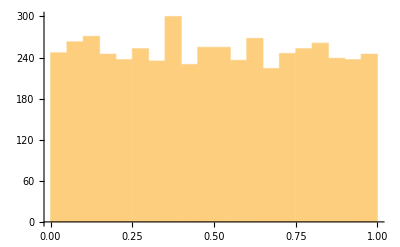

```mathematica
(* Histogram (graf) hustoty pravdepodobnosti pseudogeneratoru 5000 nahodnych cisel *)
x=RandomReal[{},5000];
Histogram@x
```

Mathematica umí generovat čísla o různých rozděleních.

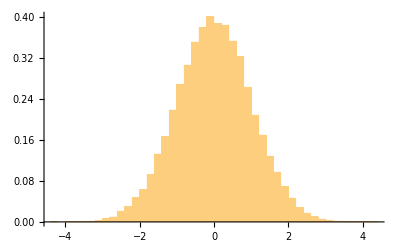

```mathematica
x=RandomVariate[NormalDistribution[],50000];
Histogram[x,50,"PDF"](* 50(může být i Automatic) - počet sloupců
	PDF - graf funkce hustoty pravděpodobosti
 *)
```

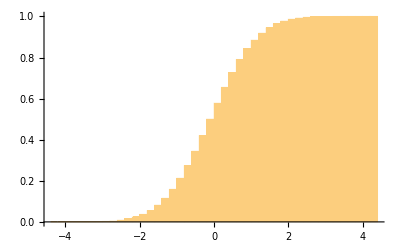

```mathematica
Histogram[x,50,"CDF"](* 50 - počet sloupců
	CDF - graf distribuční funkce
 *)
```

### Derivace

Výpočet derivace.

```mathematica
Clear@x
```

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Sin[x],{x,3}](* třetí derivace podle x *)
```

-Cos[x]

### Integrace

Výpočet integrálu

```mathematica
Integrate[x,x](* neurčitý integrál *)
```

x^2/2

```mathematica
Integrate[ⅇ^x,{x,0,2}](* určitý integrál *)
```

-1+ⅇ^2

### Řešení rovnic (jednoduché, soustavy, diferenciální)

Řešení rovnic obecně

```mathematica
NSolve[x-2 x^2+3==0,x]
```

{{x→-1.},{x→1.5}}

```mathematica
Solve[x-2 x^2+3==0,x]
```

{{x→-1},{x→3/2}}

```mathematica
Clear[x,y];
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

Soustava rovnic
4x+3y=6
2x+1y=4

```mathematica
LinearSolve[{{4,3},{2,1}},{6,4}]
```

```mathematica
{3,-2}(* x,y *)
```